# Лабораторная работа №5

## Воинов Владислав, 421701, вариант 9

### Задание 1

Решить задачу Коши для дифференциального уравнения первого порядка на отрезке :
	а) методом Эйлера-Коши с шагом  и , построить графики полученных решений;
	б) методом Рунге-Кутта 4-го порядка с шагом  и , построить графики полученных решений;
	в) с помощью функций DSolve и NDSolve, построить графики.
Сравнить все полученные решения. Сделать выводы о точности методов в зависимости от шага сетки.

Зададим функцию, начальное условие и границы отрезка:

```mathematica
f[x_, y_]:=5 Cos[y]-Sin[x]+x^2;
y0=0.5;
a=0;
b=1;
```

#### Метод Эйлера-Коши

Зададим функцию для метода Эйлера-Коши:

```mathematica
EulerCouchy[f_,a_,b_,y0_,h_]:=Module[{n,xs,ys,i,predictor},n=Round[(b-a)/h];
xs=Table[a+i h,{i,0,n}];
ys=ConstantArray[0.,n+1];
ys[[1]]=y0;
For[i=1,i<=n,i++,predictor=ys[[i]]+h f[xs[[i]],ys[[i]]];
ys[[i+1]]=ys[[i]]+h/2 (f[xs[[i]],ys[[i]]]+f[xs[[i+1]],predictor]);];
Transpose[{xs,ys}]];
```

#### Метод Рунге-Кутта

Зададим функцию для метода Рунге-Кутта:

```mathematica
RungeKutta4[f_,a_,b_,y0_,h_]:=Module[{n,xs,ys,i,k1,k2,k3,k4},n=Round[(b-a)/h];
xs=Table[a+i h,{i,0,n}];
ys=ConstantArray[0.,n+1];
ys[[1]]=y0;
For[i=1,i<=n,i++,k1=h f[xs[[i]],ys[[i]]];
k2=h f[xs[[i]]+h/2,ys[[i]]+k1/2];
k3=h f[xs[[i]]+h/2,ys[[i]]+k2/2];
k4=h f[xs[[i]]+h,ys[[i]]+k3];
ys[[i+1]]=ys[[i]]+(k1+2 k2+2 k3+k4)/6;];
Transpose[{xs,ys}]];
```

Решим  задачу Коши для данного дифференциального уравнения и сравним полученные результаты:

```mathematica
Task1[f_,y0_,h_]:=Module[{t1,t2,solN,gr1,gr2,gr3},t1=EulerCouchy[f,a,b,y0,h];
t2=RungeKutta4[f,a,b,y0,h];
solN=NDSolveValue[{y'[x]==f[x,y[x]],y[a]==y0},y,{x,a,b}];
gr1=ListLinePlot[t1,ImageSize->Large,PlotStyle->Red,PlotLegends->{"Euler-Cauchy"}];
gr2=ListLinePlot[t2,ImageSize->Large,PlotStyle->Green,PlotLegends->{"Runge-Kutta 4"}];
gr3=Plot[solN[x],{x,a,b},ImageSize->Large,PlotStyle->Black,PlotLegends->{"NDSolve"}];
{gr1,gr2,gr3}];
```

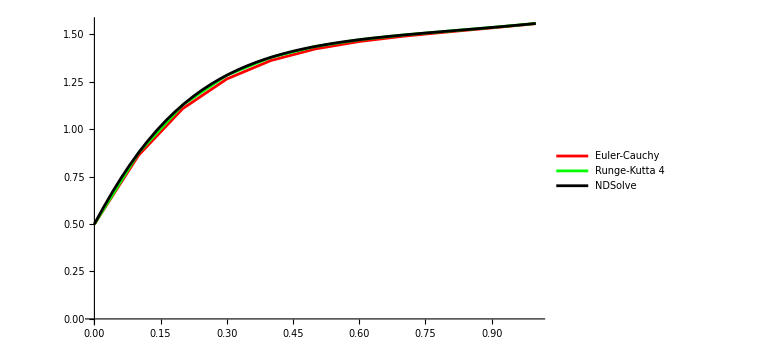

```mathematica
Show[Task1[f,y0,0.1]]
```

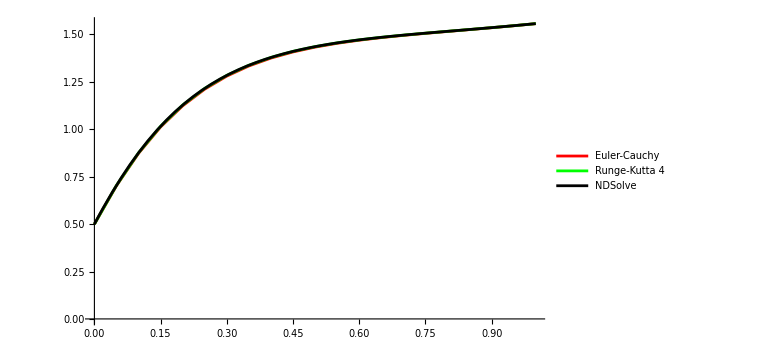

```mathematica
Show[Task1[f,y0,0.05]]
```

#### Вывод

Точность методов растёт от увеличения шага сетки.

### Задание 2

Решить задачу Коши для системы двух дифференциальных уравнений на отрезке :
	а) методом Эйлера с шагом  и , построить графики полученных решений;
	б) методом Рунге-Кутта 4-го порядка с шагом  и , построить графики полученных решений;
	в) с помощью функций DSolve и NDSolve, построить графики.
Сравнить все полученные решения.

Зададим функции, начальные условия и границы отрезков:

```mathematica
f1[x_,y_,z_]:=2-5z;
f2[x_,y_,z_]:=-3z-y;
y0=0.5;
z0=2;
```

#### Метод Эйлера

Зададим функцию для метода Эйлера:

```mathematica
Euler[f1_,f2_,a_,b_,y0_,z0_,h_]:=Module[{n,y,z,x,i},
n=(b-a)/h;
Array[y,0,n];
y[0]=y0;
Array[z,0,n];
z[0]=z0;
x[i_]:=a+i h;
For[i=0,i<n,i++,
y[i+1]=y[i]+h f1[x[i],y[i],z[i]];
z[i+1]=z[i]+h f2[x[i],y[i],z[i]];
];
{Table[{x[i],y[i]},{i,0,n-1}],Table[{x[i],z[i]},{i,0,n-1}]}
];
```

#### Метод Рунге-Кутта

Зададим функцию для метода Рунге-Кутта:

```mathematica
RungeKutta4Sys2[f1_,f2_,a_,b_,y0_,z0_,h_]:=Module[{n,y,z,x,i,k1,k2,k3,k4,r1,r2,r3,r4},
n=(b-a)/h;
Array[y,0,n];
y[0]=y0;
Array[z,0,n];
z[0]=z0;
x[i_]:=a+i h;
For[i=0,i<n,i++,
k1=h f1[x[i],y[i],z[i]];
r1=h f2[x[i],y[i],z[i]];
k2=h f1[x[i]+h/2,y[i]+k1/2,z[i]+r1/2];
r2=h f2[x[i]+h/2,y[i]+k1/2,z[i]+r1/2];
k3=h f1[x[i]+h/2,y[i]+k2/2,z[i]+r2/2];
r3=h f2[x[i]+h/2,y[i]+k2/2,z[i]+r2/2];
k4=h f1[x[i]+h,y[i]+k3,z[i]+r3];
r4=h f2[x[i]+h,y[i]+k3,z[i]+r3];
y[i+1]=y[i]+1/6(k1+2k2+2k3+k4);
z[i+1]=z[i]+1/6(r1+2r2+2r3+r4);
];
{Table[{x[i],y[i]},{i,0,n-1}],Table[{x[i],z[i]},{i,0,n-1}]}
];
```

Решим задачу Коши для данной системы дифференциальных уравнений и сравним полученные результаты:

```mathematica
Task2[f1_,f2_,y0_,z0_,h_]:=Module[{t1,t2,t3,t4,t5,gr1,gr2,gr3,gr4,y,z},
t1=Euler[f1,f2,a,b,y0,z0,h];
t2=RungeKutta4Sys2[f1,f2,a,b,y0,z0,h];
t3=DSolveValue[{y'[x]==f1[x,y[x],z[x]],z'[x]==f2[x,y[x],z[x]],y[0]==y0,z[0]==z0},{y[x],z[x]},x];
{t4,t5}=NDSolveValue[{y'[x]==f1[x,y[x],z[x]],z'[x]==f2[x,y[x],z[x]],y[0]==y0,z[0]==z0},{y,z},{x,a,b}];
gr1=ListLinePlot[t1, ImageSize->Large, PlotStyle->Red];
gr2=ListLinePlot[t2, ImageSize->Large, PlotStyle->Green];
gr3=Plot[t3,{x,a,b}, ImageSize->Large, PlotStyle->Blue];
gr4=Plot[{t4[x],t5[x]},{x,a,b}, ImageSize->Large, PlotStyle->Black];
{gr1,gr2,gr3,gr4}
];
```

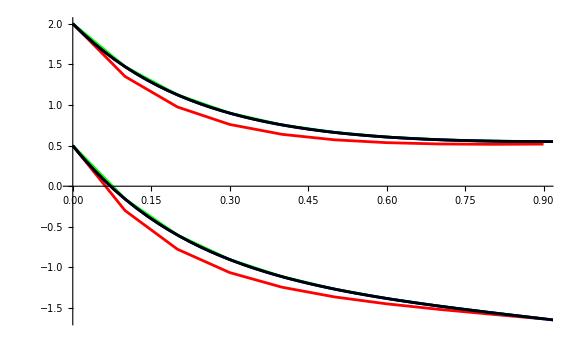

```mathematica
Show[Task2[f1,f2,y0,z0,0.1]]
```

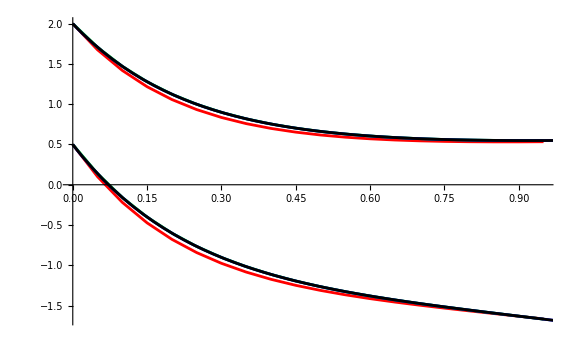

```mathematica
Show[Task2[f1,f2,y0,z0,0.05]]
```